### In order to write the Hamiltonian of the circuit, we need to write the Lagrangian first:

```mathematica
ℒ=(2 Cc ((ϕpsnail-ϕpcav)/2)^2)/2+(Ccav ϕpcav^2)/2+(2 Cc ((ϕpsnail-ϕpcav)/2)^2)/2+(Cs ϕpsnail^2)/2-ϕcav^2/(2Lcav)+α Ej Cos[ϕsnail]+3Ej Cos[(ϕext-ϕsnail)/3];
sub=Flatten[Solve[Qcav==D[ℒ,ϕpcav]&&Qsnail==D[ℒ,ϕpsnail],{ϕpcav,ϕpsnail}]];
FullSimplify[H=Qcav ϕpcav+Qsnail ϕpsnail-ℒ/.sub]
```

1/2 ((Cs Qcav^2+Ccav Qsnail^2+Cc (Qcav+Qsnail)^2)/(Ccav Cs+Cc (Ccav+Cs))+ϕcav^2/Lcav-6 Ej Cos[(ϕext-ϕsnail)/3]-2 Ej α Cos[ϕsnail])

### After a little simplify we have the Hamiltonian for the whole circuit:

```mathematica
parallel[Ca_,Cb_]:=1/(1/Ca+1/Cb)
H = (Qcav^2/2 1/(Ccav + parallel[Cc,Cs])+ϕcav^2/(2  Lcav))+(Qsnail^2/2 1/(Cs+parallel[Cc,Ccav])-α Ej Cos[ϕsnail]-3Ej Cos[(ϕext-ϕsnail)/3])+Qcav Qsnail Cc/(Ccav Cs + CsCc + Cc Ccav);
```

### Then we expand the nonlinear part:

```mathematica
Hsnail=-α Ej Cos[ϕsnail]-3Ej Cos[(ϕext-ϕsnail)/3];
Hsexp=Normal[Series[Hsnail/.{ϕsnail->ϕmin+δϕ},{δϕ,0,6}]]
```

```mathematica
-3 Ej Cos[(ϕext-ϕmin)/3]-Ej α Cos[ϕmin]+δϕ^4 (-1/648 Ej Cos[(ϕext-ϕmin)/3]-1/24 Ej α Cos[ϕmin])+1/6 δϕ^2 (Ej Cos[(ϕext-ϕmin)/3]+3 Ej α Cos[ϕmin])+(δϕ^6 (Ej Cos[(ϕext-ϕmin)/3]+243 Ej α Cos[ϕmin]))/174960+1/54 δϕ^3 (Ej Sin[(ϕext-ϕmin)/3]-9 Ej α Sin[ϕmin])+δϕ^5 (-(Ej Sin[(ϕext-ϕmin)/3])/9720+1/120 Ej α Sin[ϕmin])+δϕ
```

The first order term should equal zero, and from the second order coefficient, we can have new inductor definition:

```mathematica
Hst1= Hsexp/.{1/6  (Ej Cos[(ϕext-ϕmin)/3]+3 Ej α Cos[ϕmin])->1/(2 Lsnail)}
```

δϕ^2/(2 Lsnail)-3 Ej Cos[(ϕext-ϕmin)/3]-Ej α Cos[ϕmin]+δϕ^4 (-1/648 Ej Cos[(ϕext-ϕmin)/3]-1/24 Ej α Cos[ϕmin])+1/54 δϕ^3 (Ej Sin[(ϕext-ϕmin)/3]-9 Ej α Sin[ϕmin])+δϕ (-Ej Sin[(ϕext-ϕmin)/3]+Ej α Sin[ϕmin])

#### New Hamiltonian looks like that:

```mathematica
Hnew = (Qcav^2/2 1/(Ccav + parallel[Cc,Cs])+ϕcav^2/(2  Lcav))+(Qsnail^2/2 1/(Cs+parallel[Cc,Ccav])+δϕ^2/(2 Lsnail))+Qcav Qsnail Cc/(Ccav Cs + CsCc + Cc Ccav) + C0 +C1 δϕ + C3 δϕ^3 + C4 δϕ^4;
C0=-3 Ej Cos[(ϕext-ϕmin)/3]-Ej α Cos[ϕmin];
C1=-Ej Sin[(ϕext-ϕmin)/3]+Ej α Sin[ϕmin]=0;
C3=1/54(Ej Sin[(ϕext-ϕmin)/3]-9 Ej α Sin[ϕmin]);
C4= (-1/648 Ej Cos[(ϕext-ϕmin)/3]-1/24 Ej α Cos[ϕmin])
```

-1/648 Ej Cos[(ϕext-ϕmin)/3]-1/24 Ej α Cos[ϕmin]

### A little test here, see if we can get the same plot from the paper

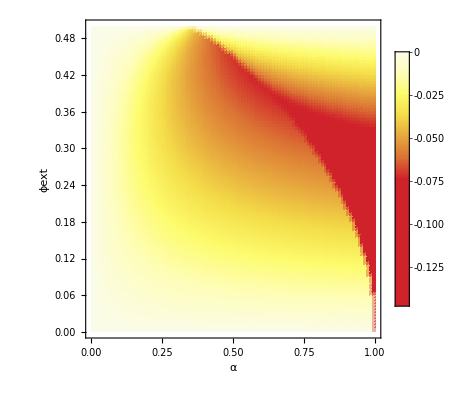

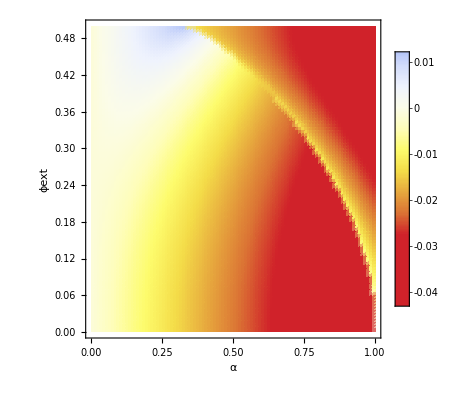

```mathematica
third=1/54 (Ej Sin[(2 π ϕext)/3-ϕmin/3]-9 Ej α Sin[ϕmin]);
fourth = (-1/648 Ej Cos[(2 π ϕext)/3-ϕmin/3]-1/24 Ej α Cos[ϕmin]);
ϕ0=2*10^-15;
i0=0.05*10^-6;
Ej = 1;
res3=Monitor[Transpose[Table[Table[third/.{α->i,ϕext->j}/.{ϕmin->ϕ}/.NSolve[{D[Hjj,ϕ]==0&&2π≥ϕ≥-2π}/.{α->i,ϕext->j},ϕ][[1]],{j,0,0.5,0.5/100}],{i,0,1,0.01}]],{ProgressIndicator[i],i}];
res4=Monitor[Transpose[Table[Table[fourth/.{α->i,ϕext->j}/.{ϕmin->ϕ}/.NSolve[{D[Hjj,ϕ]==0&&2π≥ϕ≥-2π}/.{α->i,ϕext->j},ϕ][[1]],{j,0,0.5,0.5/100}],{i,0,1,0.01}]],{ProgressIndicator[i],i}];
ListDensityPlot[
res3,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0},{0.5-Max[res3]/(Max[res3]-Min[res3]),0.5-Min[res3]/(Max[res3]-Min[res3])}]]&),PlotLegends->Automatic,
DataRange->{{0,1},{0,0.5}},FrameLabel->{"α","ϕext"},FrameStyle->Directive[Thick,14]
]
ListDensityPlot[
res4,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{1,0},{0.5-Max[res4]/(Max[res4]-Min[res4]),0.5+(-Min[res4])/(Max[res4]-Min[res4])}]]&),PlotLegends->Automatic,
DataRange->{{0,1},{0,0.5}},FrameLabel->{"α","ϕext"},FrameStyle->Directive[Thick,14]]
```

#### We have the simplified Hamiltonian :

```mathematica
H0 = ℏ ωcav(SuperDagger[a] a +1/2) + ℏ ωqubit (SuperDagger[b] b +1/2) + ℏ g (SuperDagger[a] b+a SuperDagger[b]) + ℏ g(a b  + SuperDagger[a] SuperDagger[b]);
H1 = C3 δϕ^3;
```

#### Using rotating wave approximation, we can ignore the last term, and we diagonalize the Hamiltonian.

```mathematica
Hdia = {{ωcav,g},{g, ωqubit}};
vecs = Eigenvectors[Hdia];
FullSimplify[Inverse[Transpose[vecs]].Hdia.Transpose[vecs]]//MatrixForm
```

(1/2 (ωcav-√(4 g^2+(ωcav-ωqubit)^2)+ωqubit) | 0
0 | 1/2 (ωcav+√(4 g^2+(ωcav-ωqubit)^2)+ωqubit))

```mathematica
vecs = Eigenvectors[Hdia];
n1=Norm[vecs[[1]]];
n2=Norm[vecs[[2]]];
Transpose[Inverse[{Simplify[vecs[[1]]/n1],Simplify[vecs[[2]]/n2]}]]/.{-ωcav+ωqubit->Δ}/.{(ωcav-ωqubit)->-Δ}//MatrixForm
```

(-(g √(4+Abs[(Δ+√(4 g^2+Δ^2))/g]^2))/(2 √(4 g^2+Δ^2)) | ((-Δ+√(4 g^2+(ωcav-ωqubit)^2)) √(4+Abs[(Δ+√(4 g^2+Δ^2))/g]^2))/(4 √(4 g^2+Δ^2))
(g √(4+Abs[(-Δ+√(4 g^2+(ωcav-ωqubit)^2))/g]^2))/(2 √(4 g^2+Δ^2)) | -((-Δ-√(4 g^2+(ωcav-ωqubit)^2)) √(4+Abs[(-Δ+√(4 g^2+(ωcav-ωqubit)^2))/g]^2))/(4 √(4 g^2+Δ^2)))

```mathematica
ωC=1/2(ωcav+ωqubit-√(4 g^2+Δ^2));
ωQ=1/2(ωcav+ωqubit+√(4 g^2+Δ^2));
{{λa,μa},{λb,μb}} = ({{-(g √(4+((Δ+√(4 g^2+Δ^2))/g)^2))/(2 √(4 g^2+Δ^2)), ((-Δ+√(4 g^2+Δ^2)) √(4+((Δ+√(4 g^2+Δ^2))/g)^2))/(4 √(4 g^2+Δ^2))}, {(g √(4+((-Δ+√(4 g^2+Δ^2))/g)^2))/(2 √(4 g^2+Δ^2)), -((-Δ-√(4 g^2+Δ^2)) √(4+((-Δ+√(4 g^2+Δ^2))/g)^2))/(4 √(4 g^2+Δ^2))}});
H0= ℏ ωC(SuperDagger[A] A +1/2) + ℏ ωQ (SuperDagger[B] B +1/2);
```

#### Now we can temporally go back to the anharmonic term H1 with the dressed operators:

```mathematica
b=λb A + μb B;
SuperDagger[b]=λb SuperDagger[A]+μb SuperDagger[B];
```